```mathematica
$HistoryLength = 1;
SetDirectory["D:/GitRoot/llio/Source/Optimizer/BuildPath"]

Import["../../Database/db_buildtree.m"]
<< "LatticePoset.m"

(* TODO: this doesn't handle items with no build path like doran's blade *)
dbGraph[ids__] := With[
	{es = Flatten[(#/.buildTree&) /@ {ids}, 1]}, 
	Graph[uniqueDuplicates[es] /. ({α_,β_} -> α -> β), VertexLabels->"Name"]
]
uniqueDuplicates[xs_]:= Module[{duplicates,rules},
	duplicates = First /@ Select[Tally[Flatten[xs⟦All,1⟧]], #⟦2⟧ > 1 &];
	rules      = ({#,α_} :> {# <> ToString@Unique[], α}&) /@ duplicates;
	xs /. rules
]
dbGraphI[x_String]  := dbGraphI[dbGraph[x]]
dbGraphI[x__String] := dbGraphI[dbGraph[x]]
dbGraphI[g_Graph] := Module[{rules},
	rules = Thread[VertexList[g] -> Range[VertexCount[g]]];
	{Reverse/@rules, VertexReplace[g, rules]}
	]
dbGraphI[x_] := Throw["dbGraphI: invalid parameter type"]

(*************)
(*{14783.980768,102918816000}  "The Bloodthirster","Youmuu's Ghostblade", "Infinity Edge", "Last Whisper"
g = dbGraph["The Bloodthirster","Youmuu's Ghostblade", "Infinity Edge", "Last Whisper"];*)

{grules,testScale} = dbGraphI["Youmuu's Ghostblade"]
(*grules = {5->"Avarice Blade",6->"Youmuu's Ghostblade",4->"Brawler's Gloves",3->"The Brutalizer",1->"Long Sword$42",2->"Long Sword$43"}*)
(*testScale = Graph[{1->3,2->3,3->6,4->5,5->6}, VertexLabels->"Name"]*)

(* uses vertex labels for indices instead of internal vertex index *)
adjacencyMatrixVL[g_] := Normal@SparseArray[EdgeList[g] /. ((x_ -> y_) -> ({x,y} -> 1)), 
							With[{n=VertexCount[g]},{n,n}], 0]

adjacencyMatrixVL[testScale]

le = TopologicalSort[testScale]
lattice = LatticePoset`idealLattice[testScale]

nPaths = LatticePoset`countLinearExtensions[lattice]
buildPaths2 = LatticePoset`nthLinearExtension[lattice,#]& /@ Range[0,nPaths-1]
buildPaths  = LatticePoset`allLinearExtensions[lattice] 
buildPaths == buildPaths2

testGraph = LatticePoset`idealLattice[System`Graph[{2->4,1->3,1->4,3->5}, VertexLabels->"Name"]]
LatticePoset`allLinearExtensions[testGraph]
```

D:\GitRoot\llio\Source\Optimizer\BuildPath

{{1→Avarice Blade,2→Youmuu's Ghostblade,3→Brawler's Gloves,4→The Brutalizer,5→Long Sword$9,6→Long Sword$10},-Graphics-}

{{0,1,0,0,0,0},{0,0,0,0,0,0},{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,0,1,0,0},{0,0,0,1,0,0}}

{5,3,1,6,4,2}

-Graphics-

20

{{3,1,5,6,4,2},{3,1,6,5,4,2},{3,5,1,6,4,2},{3,5,6,1,4,2},{3,5,6,4,1,2},{3,6,1,5,4,2},{3,6,5,1,4,2},{3,6,5,4,1,2},{5,3,1,6,4,2},{5,3,6,1,4,2},{5,3,6,4,1,2},{5,6,3,1,4,2},{5,6,3,4,1,2},{5,6,4,3,1,2},{6,3,1,5,4,2},{6,3,5,1,4,2},{6,3,5,4,1,2},{6,5,3,1,4,2},{6,5,3,4,1,2},{6,5,4,3,1,2}}

{{3,1,5,6,4,2},{3,1,6,5,4,2},{3,5,1,6,4,2},{3,5,6,1,4,2},{3,5,6,4,1,2},{3,6,1,5,4,2},{3,6,5,1,4,2},{3,6,5,4,1,2},{5,3,1,6,4,2},{5,3,6,1,4,2},{5,3,6,4,1,2},{5,6,3,1,4,2},{5,6,3,4,1,2},{5,6,4,3,1,2},{6,3,1,5,4,2},{6,3,5,1,4,2},{6,3,5,4,1,2},{6,5,3,1,4,2},{6,5,3,4,1,2},{6,5,4,3,1,2}}

True

-Graphics-

{{2,1,4,3,5},{2,1,3,4,5},{2,1,3,5,4},{1,2,4,3,5},{1,2,3,4,5},{1,2,3,5,4},{1,3,2,4,5},{1,3,2,5,4},{1,3,5,2,4}}

```mathematica
Import["../../Database/db_layout.m"]; (*itemDatabaseFields, itemDatabaseRules *)

database  = Import["../../Database/items.dat", "Table"];
passives  = Import["../../Database/passives.dat", "Table"];
ids       = #⟦"F_ID" /.itemDatabaseRules⟧& /@ database;
names     = Import["../../Database/names.dat", "List"];
name2id   = Thread[names -> ids];
id2index  = Thread[ids -> Range[Length[ids]]];

convert[p_] := StringReplace[p, "$" ~~ __ -> ""] /. name2id /. id2index
node2id = grules /. ((n_ -> p_) :> (n -> convert[p]));

Normal@SparseArray[node2id]
LatticePoset`export[lattice]
```

{103,138,21,131,15,15}

{MaxCombo→6,MaxOutDegree→3,CVertex→{0,0,4,16,32,5,20,36,48,21,37,52,56,53,60,61,63},CAdjacency→{{0,0,0},{2,3,4},{5,6,7},{6,8,0},{7,8,0},{9,10,0},{9,11,0},{10,11,0},{11,12,0},{13,0,0},{13,0,0},{13,14,0},{14,0,0},{15,0,0},{15,0,0},{16,0,0},{0,0,0}},CIdeals→{{0,0,0},{3,5,6},{1,5,6},{3,6,0},{3,5,0},{5,6,0},{1,6,0},{1,5,0},{3,4,0},{6,0,0},{5,0,0},{1,4,0},{3,0,0},{4,0,0},{1,0,0},{2,0,0},{0,0,0}}}

```mathematica
(***********************************)
ASOFFSET    = (-0.04);
ASLVPER     = (0.0322);
ASBASE      = (0.625/(1+ASOFFSET));

CALCATTACKSPEED[LV_,GEAR_] :=
	Min[2.5, ASBASE * (1+(ASLVPER*(LV-1)) + GEAR)]

CALCCRIT[B_,C_] := 1.0 + (1.0 + B) * Min[1.0, C]

CALCARMORMITIGATION[ARMOR_, APP_, APF_] := 100/(100+((ARMOR*(1-APP))-APF))

CALCAD[AD_,HP_,HPRATIO_] := 70+AD+(HP*HPRATIO)

FORMULADPS[ARMOR_,LV_] := 
	CALCARMORMITIGATION[ARMOR,"F_ARMORPEN_PERCENT", "F_ARMORPEN_FLAT"] *
	CALCAD["F_AD", "F_HP", "F_HP2AD"] *
	CALCCRIT["F_CRIT_BONUS", "F_CRIT_CHANCE"] *
	CALCATTACKSPEED[LV, "F_ATTACK_SPEED"]

FORMULAABILITY[ARMOR_, SCALE_] := 
	CALCARMORMITIGATION[ARMOR,"F_ARMORPEN_PERCENT", "F_ARMORPEN_FLAT"] *  
	CALCAD["F_AD", "F_HP", "F_HP2AD"] * SCALE

FORMULATOTAL = FORMULAABILITY["C_ENEMY_ARMOR", "C_AD_RATIO"] +
			  (FORMULADPS["C_ENEMY_ARMOR", "C_LEVEL"] * "C_TIMEFRAME");

configFields = {"C_TIMEFRAME", "C_AD_RATIO", "C_ENEMY_ARMOR", "C_LEVEL", "C_MAXCOST"};

dpsFormula[cfg_,db_] := Block[{rules},
	rules[symbol_, fields_] := MapIndexed[#1 -> symbol⟦First@#2⟧&, fields];
	FORMULATOTAL /. Join[rules[cfg, configFields],rules[db, itemDatabaseFields]]
]

(* TODO: this doesn't remove duplicate passives, but it needs to *)
getMergedStats[i_] := Block[{xs = database⟦i⟧, index},
	index = xs⟦("F_PASSIVE" /. itemDatabaseRules)⟧; (* zero based index *)
	If[index ≠ 0, 
		xs + PadLeft[passives⟦index+1⟧, Length[passives⟦index+1⟧] + itemPassiveSyncOffset], 
		xs
	]
]

tally[{xs_,stats_},i_] := With[{combined=stats + getMergedStats[i]}, 
	{Append[xs, dpsFormula[{3,3.4,100,18,15000}, combined]], combined}
	]

getDPS[path_] :=  Fold[tally, {{}, ConstantArray[0,Length[itemDatabaseFields]]}, path]
getCosts[path_] := Map[database⟦#⟧⟦"F_UPGRADE_COST" /. itemDatabaseRules⟧&, path]


metricAreaDPS[path_] := With[{dps=First@getDPS[path], costs=getCosts[path]}, Total[dps * costs] / 1000]

selectBest[p_, metric_] := p⟦First@Ordering[metric /@ p,1,GreaterEqual]⟧ 

buildPaths = buildPaths /. node2id
(*ids⟦#⟧& /@ ({6,5,4,3,1,2} /. node2id) 
getDPS/@ {{6,5,4,3,1,2} /. node2id}
*)
metricAreaDPS /@ buildPaths
best = selectBest[buildPaths,metricAreaDPS]
best /. grules
Position[buildPaths, best]
```

{{21,103,15,15,131,138},{21,103,15,15,131,138},{21,15,103,15,131,138},{21,15,15,103,131,138},{21,15,15,131,103,138},{21,15,103,15,131,138},{21,15,15,103,131,138},{21,15,15,131,103,138},{15,21,103,15,131,138},{15,21,15,103,131,138},{15,21,15,131,103,138},{15,15,21,103,131,138},{15,15,21,131,103,138},{15,15,131,21,103,138},{15,21,103,15,131,138},{15,21,15,103,131,138},{15,21,15,131,103,138},{15,15,21,103,131,138},{15,15,21,131,103,138},{15,15,131,21,103,138}}

{1010.39,1010.39,1019.49,1027.98,1061.42,1019.49,1027.98,1061.42,1028.95,1037.44,1070.88,1046.42,1079.86,1113.39,1028.95,1037.44,1070.88,1046.42,1079.86,1113.39}

{15,15,131,21,103,138}

{15,15,131,21,103,138}

{{14},{20}}

```mathematica
analyze[path_, color_] := Block[{plots,dps,costs,stats,plotRules,chart},
	costs = Accumulate@getCosts[path];
	{dps,stats} = getDPS[path];
	plots = Prepend[Thread[{dps,costs}], {0,0}];
	plotRules = Map[#⟦2⟧ -> #⟦1⟧&, plots];
	chart = DiscretePlot[x /. plotRules, {x, plots⟦All, 2⟧}, ExtentSize -> Full, ExtentMarkers -> {"Filled", "Empty"}, 
		ColorFunction -> Function[{x,y}, ColorData["SolarColors",color]]];
	chart
]

(*
colors = Accumulate[ConstantArray[1 / Length[paths], Length[paths]]];
ListAnimate[Apply[analyze,#]& /@ Thread[{paths,colors}]] 
*)
```

```mathematica
(* C Export *)
Off[General::partd]
CForm[dpsFormula[CFG, STAT]]
On[General::partd]
```

(100*CFG[2]*(70 + STAT[5] + STAT[11]*STAT[12]))/(100 - STAT[9] + CFG[3]*(1 - STAT[10])) + 
   (100*Min(2.5,0.6510416666666667*(1 + 0.0322*(-1 + CFG[4]) + STAT[8]))*CFG[1]*(1. + Min(1.,STAT[6])*(1. + STAT[7]))*(70 + STAT[5] + STAT[11]*STAT[12]))/(100 - STAT[9] + CFG[3]*(1 - STAT[10]))

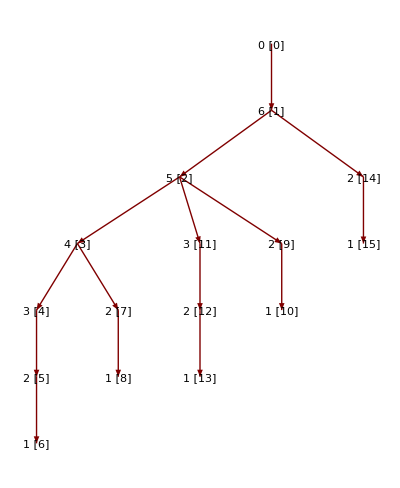

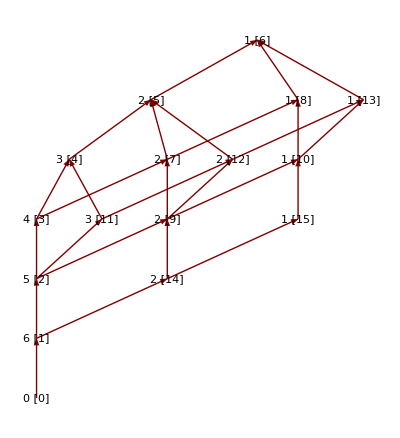

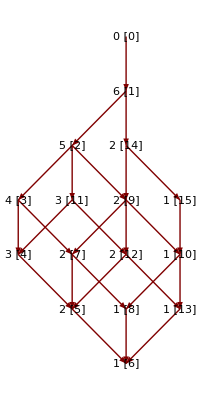

-Graphics-

-Graphics-

True

True

```mathematica
idealtree = {
{"0 [0]" -> "6 [1]", 6},
{"6 [1]" -> "5 [2]", 5},
{"5 [2]" -> "4 [3]", 4},
{"4 [3]" -> "3 [4]", 3},
{"3 [4]" -> "2 [5]", 2},
{"2 [5]" -> "1 [6]", 1},
{"4 [3]" -> "2 [7]", 2},
{"2 [7]" -> "1 [8]", 1},
{"5 [2]" -> "3 [11]", 3},
{"3 [11]" -> "2 [12]", 2},
{"2 [12]" -> "1 [13]", 1},
{"5 [2]" -> "2 [9]", 2},
{"2 [9]" -> "1 [10]", 1},
{"6 [1]" -> "2 [14]", 2},
{"2 [14]" -> "1 [15]", 1}
};
ideallattice = {
{"0 [0]" -> "6 [1]", 6},
{"6 [1]" -> "5 [2]", 5},
{"5 [2]" -> "4 [3]", 4},
{"4 [3]" -> "3 [4]", 3},
{"3 [4]" -> "2 [5]", 2},
{"2 [5]" -> "1 [6]", 1},
{"4 [3]" -> "2 [7]", 2},
{"2 [7]" -> "2 [5]", 3},
{"2 [7]" -> "1 [8]", 1},
{"1 [8]" -> "1 [6]", 3},
{"5 [2]" -> "3 [11]", 3},
{"3 [11]" -> "3 [4]", 4},
{"3 [11]" -> "2 [12]", 2},
{"2 [12]" -> "2 [5]", 4},
{"2 [12]" -> "1 [13]", 1},
{"1 [13]" -> "1 [6]", 4},
{"5 [2]" -> "2 [9]", 2},
{"2 [9]" -> "2 [12]", 3},
{"2 [9]" -> "2 [7]", 4},
{"2 [9]" -> "1 [10]", 1},
{"1 [10]" -> "1 [8]", 4},
{"1 [10]" -> "1 [13]", 3},
{"6 [1]" -> "2 [14]", 2},
{"2 [14]" -> "2 [9]", 5},
{"2 [14]" -> "1 [15]", 1},
{"1 [15]" -> "1 [10]", 5}
};
latticeEdges = {
{{1,2,3,4,5,6} -> {1,3,4,5,6}, 2},
{{1,3,4,5,6} -> {1,3,5,6}, 4},
{{1,3,5,6} -> {1,3,5}, 6},
{{1,3,5} -> {1,3}, 5},
{{1,3} -> {3}, 1},
{{3} -> {}, 3},
{{1,3,5} -> {3,5}, 1},
{{3,5} -> {3}, 5},
{{3,5} -> {5}, 3},
{{5} -> {}, 5},
{{1,3,5,6} -> {1,3,6}, 5},
{{1,3,6} -> {1,3}, 6},
{{1,3,6} -> {3,6}, 1},
{{3,6} -> {3}, 6},
{{3,6} -> {6}, 3},
{{6} -> {}, 6},
{{1,3,5,6} -> {3,5,6}, 1},
{{3,5,6} -> {3,6}, 5},
{{3,5,6} -> {3,5}, 6},
{{3,5,6} -> {5,6}, 3},
{{5,6} -> {5}, 6},
{{5,6} -> {6}, 5},
{{1,3,4,5,6} -> {3,4,5,6}, 1},
{{3,4,5,6} -> {3,5,6}, 4},
{{3,4,5,6} -> {4,5,6}, 3},
{{4,5,6} -> {5,6}, 4}
};

(*Automatic, ls⟦1⟧⟦1⟧⟦1⟧,*)
(*TreePlot[idealtree, Automatic, idealtree⟦1⟧⟦1⟧,VertexLabeling -> True]*)
TreePlot[idealtree, Automatic, idealtree⟦1⟧⟦1⟧⟦1⟧,VertexLabeling -> True]
TreePlot[ideallattice, Automatic, "1 [6]",VertexLabeling -> True, EdgeLabeling->True]
LayeredGraphPlot[idealtree, VertexLabeling -> True];
LayeredGraphPlot[ideallattice, VertexLabeling -> True, EdgeLabeling->Automatic]
LayeredGraphPlot[latticeEdges,  VertexLabeling -> True];
latticeC = Graph[Sort[latticeEdges /. ({a_ -> b_, c_}) :> Labeled[Sort[b] -> Sort[a],c]], VertexLabels->"Name"]
lattice

EdgeList[lattice] == EdgeList[latticeC]
VertexList[lattice] == VertexList[latticeC]
```